ω_0

4.42945

α_theta

0.0648

α_phi

0.0648

a_u

0.2

a_v

0.

a_w

0.

β_u

a

β_v

a

β_w

2 a

P_theta

0.

P_phi

0.

Sin[θ[t]]+0.0648 θ'[t]-Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2+θ''[t]==0.-0.2 a^2 Cos[a t] Cos[θ[t]] Sin[ϕ[t]]

(0.0648 ϕ'[t])/(0.5-0.5 Cos[2 θ[t]])+2 Cot[θ[t]] θ'[t] ϕ'[t]+ϕ''[t]==0.-0.2 a^2 Cos[a t] Cos[ϕ[t]] Csc[θ[t]]

Power::infy: Infinite expression 1/0. encountered.

NDSolveValue::nlnum: The function value {0.612003,0.0446847,3.35822×10^-9,ComplexInfinity} is not a list of numbers with dimensions {4} at {t,θ[t],θ'[t],ϕ[t],ϕ'[t]} = {517.196,4.98992×10^-9,0.612003,-1.9453,3.35822×10^-9}.

Power::infy: Infinite expression 1/0. encountered.

NDSolveValue::nlnum: The function value {1.1898,-0.0108379,8.50188×10^-8,ComplexInfinity} is not a list of numbers with dimensions {4} at {t,θ[t],θ'[t],ϕ[t],ϕ'[t]} = {26.2549,-4.53614×10^-9,1.1898,-0.764728,8.50188×10^-8}.

Power::infy: Infinite expression 1/0. encountered.

NDSolveValue::nlnum: The function value {0.932741,0.124043,3.0247×10^-8,ComplexInfinity} is not a list of numbers with dimensions {4} at {t,θ[t],θ'[t],ϕ[t],ϕ'[t]} = {374.65,1.369×10^-9,0.932741,-17.2604,3.0247×10^-8}.

NDSolveValue::ndcf: Repeated convergence test failure at t == 687.52; unable to continue.

NDSolveValue::ndcf: Repeated convergence test failure at t == 276.888; unable to continue.

NDSolveValue::ndcf: Repeated convergence test failure at t == 244.283; unable to continue.

NDSolveValue::ndcf: Repeated convergence test failure at t == 453.627; unable to continue.

NDSolveValue::ndcf: Repeated convergence test failure at t == 671.784; unable to continue.

NDSolveValue::ndcf: Repeated convergence test failure at t == 375.092; unable to continue.

Power::infy: Infinite expression 1/0. encountered.

NDSolveValue::nlnum: The function value {1.15678,0.0588742,-1.49865×10^-8,ComplexInfinity} is not a list of numbers with dimensions {4} at {t,θ[t],θ'[t],ϕ[t],ϕ'[t]} = {545.851,2.5923×10^-9,1.15678,26.8489,-1.49865×10^-8}.

NDSolveValue::ndcf: Repeated convergence test failure at t == 429.281; unable to continue.

Power::infy: Infinite expression 1/0. encountered.

NDSolveValue::nlnum: The function value {-0.485389,0.0913365,-5.44733×10^-9,ComplexInfinity} is not a list of numbers with dimensions {4} at {t,θ[t],θ'[t],ϕ[t],ϕ'[t]} = {171.332,2.06248×10^-9,-0.485389,3.51178,-5.44733×10^-9}.

NDSolveValue::ndcf: Repeated convergence test failure at t == 126.393; unable to continue.

NDSolveValue::ndcf: Repeated convergence test failure at t == 515.68; unable to continue.

NDSolveValue::ndcf: Repeated convergence test failure at t == 724.183; unable to continue.

Power::infy: Infinite expression 1/0. encountered.

NDSolveValue::nlnum: The function value {0.309016,-0.085432,2.43627×10^-8,ComplexInfinity} is not a list of numbers with dimensions {4} at {t,θ[t],θ'[t],ϕ[t],ϕ'[t]} = {534.748,-5.10834×10^-9,0.309016,22.655,2.43627×10^-8}.

{1}
 |  |  |  |

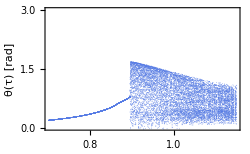

```mathematica
ClearAll["Global`*"] 

tend=1100;                       (* max time for the independent variable in ND Solve in s*)



l=0.5;                             (* Length of pendulum l*)
m=1.32;                        (*Mass at end of Pendulum in kg*)
g=9.81;                           (*Gravitational Acceleration in m/s^2*)


Subscript[ω, n]= Sqrt[g/l]  ;       (*Frequency for Excitation close to Natural Frequency*)

freq=Subscript[ω, n];
Subscript[Ω, u]=freq  ;                           (*Frequency for Excitation for Coordinate System in Direction of u in 1/s*)
Subscript[Ω, v]= freq;                              (*Frequency for Excitation for Coordinate System in Direction of v in 1/s*)
Subscript[Ω, w]=2* freq   ;                    (*Frequency for Excitation for Coordinate System in Direction of w in 1/s*)


Subscript[U, 0]=0.1;                        (*Amplitude u in m *)
Subscript[V, 0]=0;                       (*Amplitude v in m*)
Subscript[W, 0]=0;                      (*Amplitude w in m*) 




(*Passive Damping*)

Subscript[ζ, θ] =0.0324;                                (*Damping ratio *)
Subscript[ζ, ϕ] =0.0324;                                (*Damping ratio*)





(*Active power take off*)

Subscript[T, θ]=0.0;                                   (*Torque take off in Nm  *)
Subscript[T, ϕ]=0.0    ;                                  (*Torque take off in Nm*)
(*Dimensionless Parameters*)

"ω_0"
Subscript[ω, 0]=Sqrt[g/l]


"α_theta"
Subscript[α, theta]=2 Subscript[ζ, θ] Subscript[ω, n]/Subscript[ω, 0]
"α_phi"
Subscript[α, phi]=2 Subscript[ζ, ϕ] Subscript[ω, n]/Subscript[ω, 0]




"a_u"
Subscript[a, u]=Subscript[U, 0]/l

"a_v"
Subscript[a, v]=Subscript[V, 0]/l

"a_w"
Subscript[a, w]=Subscript[W, 0]/l



"β_u"
Subscript[β, u]=a(*Subscript[Ω, u]/Subscript[ω, 0]*)
"β_v"
Subscript[β, v]=a(*Subscript[Ω, v]/Subscript[ω, 0]*)
"β_w"
Subscript[β, w]=2*a(*Subscript[Ω, w]/Subscript[ω, 0]*)




"P_theta"
Subscript[P, theta]=Subscript[T, θ]/(m l^2 Subscript[ω, 0]^2)
"P_phi"
Subscript[P, phi]=Subscript[T, ϕ]/(m l^2 Subscript[ω, 0]^2)
(*Initial conditions*)
icthe=0.42;           (*θ[0]   π/4*)
icphi=0.42;                       (*ϕ[0]   0*)
dicthe=0.42;                          (*θ'[0]   0*)
dicphi=0.42;                       (*ϕ'[0]   π/4*)

(*ODEs*)
eqn1dim=Sin[θ[t]]+Subscript[α, theta] θ'[t]-Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2+θ''[t]==-Cos[t Subscript[β, u]] Cos[θ[t]] Sin[ϕ[t]] Subscript[a, u] Subscript[β, u]^2+Cos[t Subscript[β, v]] Cos[θ[t]] Cos[ϕ[t]] Subscript[a, v] Subscript[β, v]^2+Cos[t Subscript[β, w]] Sin[θ[t]] Subscript[a, w] Subscript[β, w]^2-(Subscript[P, theta] 2)/π(ArcTan[(θ'[t]/0.01)])


eqn2dim=(Subscript[α, phi] ϕ'[t])/(0.5-0.5 Cos[2 θ[t]])+2 Cot[θ[t]] θ'[t] ϕ'[t]+ϕ''[t]==-Cos[t Subscript[β, u]] Cos[ϕ[t]] Csc[θ[t]] Subscript[a, u] Subscript[β, u]^2-Cos[t Subscript[β, v]] Csc[θ[t]] Sin[ϕ[t]] Subscript[a, v] Subscript[β, v]^2-(Sign[ϕ'[t]] Subscript[P, phi])/(0.5-0.5 Cos[2 θ[t]])



min=0.7;
max=1.15;
delta=0.001;

tab1=ParallelTable[{sol,points}=Reap@NDSolveValue[{eqn1dim,eqn2dim,θ[0]==icthe,ϕ[0]==icphi,θ'[0]==dicthe,ϕ'[0]==dicphi,WhenEvent[θ'[t]<0,If[t>800,Sow[θ[t]]]]},{θ,ϕ},{t,0,tend}];
{a,#}&/@Union[Flatten[points]],{a,min,max,delta}]
bif=ListPlot[{Flatten[tab1,1]}, PlotStyle->{PointSize[0.000000001]},LabelStyle->{FontFamily->"Times New Roman",FontSize->11},PlotTheme->{"Scientific","BoldColor","ItalicLabels","Frame"},FrameLabel ->{"β [-]","θ(τ) [rad]"},ImageSize->250,PlotRange->{{0.7,1.15},{0,3}}]
```